```mathematica
normalizedBgCorrectedGFP = N[
normalizeByInitialColValue[
subtractOneColFromAllColAndPositify[gfpData,50 ]
]
];
```

```mathematica
normalizedBgCorrectedRFP = N[
normalizeByInitialColValue[
subtractOneColFromAllColAndPositify[gfpData,39 ]
]
];
```

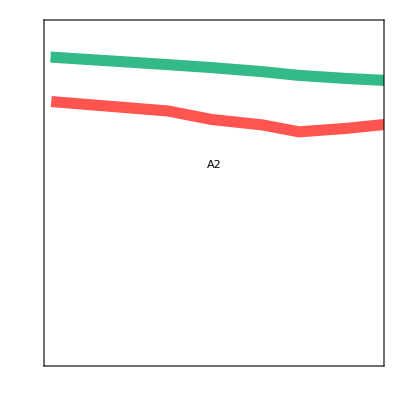

```mathematica
generateCombinedPlotOfColumn[ DevideElementWise[gfpData, odData], DevideElementWise[rfpData,odData], 6]
```

```mathematica
SystemOpen["myPlot.pdf"]
```

```mathematica
rfpData//MatrixForm
```

```mathematica
DevideElementWise[rfpData, odData]//MatrixForm
```

```mathematica
correctedODData = subtractOneColFromAllColAndPositify[odData, 12];
```

```mathematica
makePdfGfpRfp[
DevideElementWise[gfpData, correctedODData], DevideElementWise[rfpData, correctedODData], 
8, 12]
```

myPlot.pdf

```mathematica
SystemOpen["myPlot.pdf"]
```

```mathematica
SystemOpen["myPlot.pdf"]
```

```mathematica
SystemOpen["myPlot.pdf"]
```